```mathematica
m[f_]:=22.5-2.5Log[10,f];(*Convert maggy to mag, from SDSS*)
```

```mathematica
Msun=4.83;
Lsun=3.828*10^26;
Ls[Ms_]:= ⅇ^(-0.9210340371976184 Ms+0.9210340371976184 Msun) Lsun^(1.`15.653559774527023);
```

```mathematica
data=Import["/home/sean/qso_morpho/qso_flux.csv"][[2;;-1]];
```

```mathematica
LU=Table[
{
data[[i,6]],
Ls[
m[
data[[i, 4]]10^-9
]
]
},
{i,1,Length[data]}
]
```

{{0.0306827,8.68448×10^11},{-0.0000673889,1.58539×10^12},534889,{-0.000391281,1.07936×10^11},{0.0000909589,1.57858×10^11}}
 |  |  |  |

```mathematica
SFRU=Table[
{
LU[[i,1]],
LU[[i, 2]]/(5.9*10^21)
},
{i,1,Length[LU]}
]
```

{{0.0306827,1.47195×10^-10},{-0.0000673889,2.68711×10^-10},{2.07228,2.25894×10^-10},{0.000102535,1.85776×10^-10},{-0.000178665,2.83441×10^-10},{2.07038,2.04208×10^-10},{0.0306716,1.37834×10^-10},{2.0701,1.7095×10^-10},{0.0306699,1.59902×10^-10},{1.97146,2.24041×10^-10},{1.97571,1.36365×10^-10},{-0.000392538,6.53837×10^-10},534869,{3.14222,7.95817×10^-12},{2.56299,1.18164×10^-10},{3.13189,3.3303×10^-11},{2.21429,2.34401×10^-11},{0.161048,1.66588×10^-11},{2.36941,1.02407×10^-11},{2.35079,1.0025×10^-11},{0.693136,1.07641×10^-11},{2.3223,7.60849×10^-12},{-0.000226134,4.34021×10^-11},{-0.000391281,1.82943×10^-11},{0.0000909589,2.67556×10^-11}}
 |  |  |  |

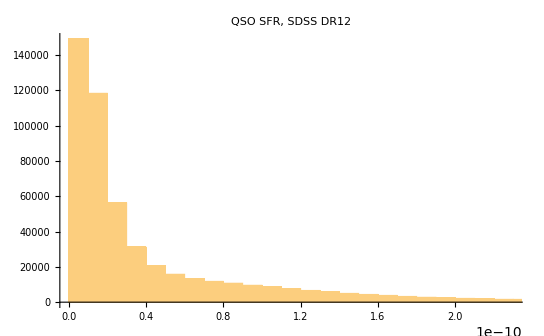

```mathematica
Histogram[
SFRU[[All,2]],
PlotLabel->"QSO SFR, SDSS DR12"
]
```

```mathematica
binSFRU={
Select[SFRU,#[[1]]>0&&#[[1]]<1&],
Select[SFRU,#[[1]]>1&&#[[1]]<2&],
Select[SFRU,#[[1]]>2&&#[[1]]<3&],
Select[SFRU,#[[1]]>3&&#[[1]]<4&],
Select[SFRU,#[[1]]>4&&#[[1]]<5&],
Select[SFRU,#[[1]]>5&&#[[1]]<6&],
Select[SFRU,#[[1]]>6&&#[[1]]<7&],
Select[SFRU,#[[1]]>7&&#[[1]]<8&]
}
```

{{{0.0306827,1.47195×10^-10},{0.000102535,1.85776×10^-10},162906,{0.693136,1.07641×10^-11},{0.0000909589,2.67556×10^-11}},6,{1}}
 |  |  |  |

```mathematica
dZ=0.5;
binMeanSFRU=Table[
{
z,
Mean[Select[SFRU, #[[1]]>z&&#[[1]]<z+dZ&][[All,2]]]
},
{z,0,8,dZ}
]
```

{{0.,8.51962×10^-11-1.99813×10^-29 ⅈ},{0.5,7.44485×10^-11-8.55685×10^-30 ⅈ},{1.,1.28571×10^-10-5.12533×10^-30 ⅈ},{1.5,9.16084×10^-11-7.63878×10^-30 ⅈ},{2.,3.81403×10^-11-1.44563×10^-29 ⅈ},{2.5,2.5782×10^-11-1.88712×10^-29 ⅈ},{3.,1.11867×10^-11-9.04149×10^-29 ⅈ},{3.5,2.50915×10^-12-2.22663×10^-28 ⅈ},{4.,1.71689×10^-12-2.44112×10^-28 ⅈ},{4.5,2.63098×10^-12-2.08146×10^-28 ⅈ},{5.,1.19375×10^-11-1.43924×10^-28 ⅈ},{5.5,1.35314×10^-11-2.29425×10^-28 ⅈ},{6.,8.80855×10^-12-1.29195×10^-28 ⅈ},{6.5,3.68443×10^-11-8.25435×10^-28 ⅈ},{7.,7.86516×10^-12},{7.5,Mean[{}]},{8.,Mean[{}]}}

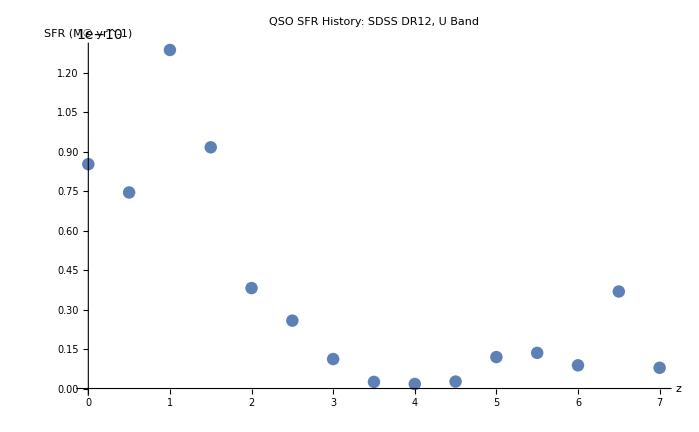

```mathematica
ListPlot[
binMeanSFRU,
PlotLabel->"QSO SFR History: SDSS DR12, U Band",
AxesLabel->{"z", "SFR (M☉ yr^-1)"}
]
```

```mathematica
Select[SFRU,Im[#[[2]]]≠0&]
```

{{1.40736,-1.91141×10^-13-6.14757×10^-29 ⅈ},{0.0000494911,-3.30087×10^-13-1.06164×10^-28 ⅈ},{4.3999,-3.33129×10^-12-1.07143×10^-27 ⅈ},16626,{2.37666,-4.13745×10^-12-1.33071×10^-27 ⅈ},{2.32716,-4.13358×10^-13-1.32946×10^-28 ⅈ},{2.99852,-8.91762×10^-12-2.86813×10^-27 ⅈ}}
 |  |  |  |